# Vesicle Flux analysis

#### Version 1 (2015-06-08) by Karolis

```mathematica
(* run this when everything fails with Shift+Enter*)
Quit[];
```

## Under the hood (peek if you dare!)

```mathematica
SetDirectory@NotebookDirectory[];

(*York fit method*)
ortlinfit[data_?MatrixQ,errs_?MatrixQ]:=Module[{n=Length[data],c,ct,dk,dm,k,m,p,s,st,ul,vl,w,wt,xm,ym},(*yes,I know I could have used FindFit[] for this...*){ct,st,k}=Flatten[MapAt[Normalize[{1,#}]&,NArgMin[Norm[Function[{x,y},y-m x-k]@@@data],{m,k}],1]];
(*find orthogonal regression coefficients*){c,s,p}=FindArgMin[{Total[(data.{-s,c}-p)^2/((errs^2).{s^2,c^2})],c^2+s^2==1},{{c,ct},{s,st},{p,k/ct}}];
(*slope and intercept*){m,k}={s,p}/c;
wt=1/errs^2;w=(Times@@@wt)/(wt.{1,m^2});
{xm,ym}=w.data/Total[w];
ul=data[[All,1]]-xm;vl=data[[All,2]]-ym;
(*uncertainties in slope and intercept*)dm=w.(m ul-vl)^2/w.ul^2/(n-2);
dk=dm (w.data[[All,1]]^2/Total[w]);
{Function[x,Evaluate[{m,k}.{x,1}]],Sqrt[{dm,dk}]}]/;Dimensions[data]===Dimensions[errs]

LinearModelFitYork::usage = 
"LinearModelFitYork[{{x,y},...}, \"Errors\"-> err] will perform Krystek/Anton and York linear regression fit:
http://iopscience.iop.org/0957-0233/18/11/025/
http://www.nrcresearchpress.com/doi/abs/10.1139/p66-090#.VXYHm9SrT2Q

\"Errors\" can be supplied with:
	Automatic - assumes 5% error variation in X and Y
	None - no errors in x and y
	p_NumberQ - assumes the erros are p fraction of the data
	{pX_NumberQ, pY_NumberQ} - assumes the erros are {pX,pY} fraction of the data
	{errY1,errY2,...} - errors only in Y
	{{errX1,errY1},...} - errors in x and y

Output: {fitted fn: y=A*x+B, {error in A, error in B} }";

LinearModelFitYork::errBadInput = "Did not recognise \"Errors\" input consult docs";
LinearModelFitYork::errFormatData = "Input data must be a Nx2 matrix";
LinearModelFitYork::errFormatErrors = "\"Errors\"  must be a convertable to Nx2 matrix";
LinearModelFitYork::errErrorsNoZeros = "\"Errors\" can't contain zero elements";

Options[LinearModelFitYork]={
"Errors"->Automatic
};

LinearModelFitYork[data_?MatrixQ,opts:OptionsPattern[] ]:= Module[
{checkErrors, compute, er},

compute[errs_]:= If[   Dimensions[data]⟦2⟧ ==2,
ortlinfit[ data, checkErrors[errs]],
(*else*)  Message[LinearModelFitYork::errFormatData]
];

checkErrors[errs_]:= If[ Dimensions[errs] == Dimensions[data],
If[ !MemberQ[errs,0.0,2],
errs,
 Throw@Message[LinearModelFitYork::errErrorsNoZeros]],
Throw@ Message[LinearModelFitYork::errFormatErrors] ];

Switch[ er= OptionValue["Errors"],
Automatic, compute[Abs[data*0.05+$MinMachineNumber]],
None,  compute[Abs[data*0.0+$MinMachineNumber]] ,
_?NumberQ,  compute[Abs[data*er+$MinMachineNumber]],
{_?NumberQ,_?NumericQ},   
 compute[Abs[Transpose@{data⟦All,1⟧*er⟦1⟧, data⟦All,2⟧*er⟦2⟧}+$MinMachineNumber]],
_?VectorQ, 
           compute[Abs[Transpose@{data⟦All,1⟧*0.0+$MinMachineNumber, N@er}]],
_?MatrixQ,compute[N@er],
_, Message[LinearModelFitYork::errBadInput]
]
]
```

#### Helpers

```mathematica
truncate[list_] := DeleteCases[list, ""];

StandardError[data_]:= StandardDeviation[data] / Sqrt[Length[data]];

showScatterPlot[]:= Show[
(*first set t=0 - Blue*)
ListPlot[Transpose@{r0,i0}, PlotStyle->Blue],
Plot[fit0[r],{r, Min[r0], Max[r0]},PlotStyle->Blue],
(*66% confidence interval*)
(*Plot[fit0[r]+σ0,{r, Min[r0], Max[r0]},
PlotStyle->Directive[Blue, Dashed, AbsoluteThickness[0.9]]
],
Plot[fit0[r]-σ0,{r, Min[r0], Max[r0]},
PlotStyle->Directive[Blue, Dashed, AbsoluteThickness[0.9]]
],*)
(*Second set t=1 - Red*)
ListPlot[Transpose@{r1,i1}, PlotStyle->Red],
Plot[fit1[r],{r, Min[r1], Max[r1]},PlotStyle->Red],
(*66% confidence interval*)
(*Plot[fit1[r]+σ1,{r, Min[r1], Max[r1]},
PlotStyle->Directive[Red, Dashed, AbsoluteThickness[0.9]]
],
Plot[fit1[r]-σ1,{r, Min[r1], Max[r1]},
PlotStyle->Directive[Red, Dashed, AbsoluteThickness[0.9]]
],*)

Frame-> True,
FrameLabel->{"R (μm)","ΔI"},
ImageSize-> 400,
FrameStyle-> Directive[AbsoluteThickness[0.8], FontSize->13, Black]
]
```

#### Main

```mathematica
runAnalysis[file_String, distance_]:= Module[
{},

raw = Import[file];
If[ MatrixQ[raw], Print["loaded file: "<>file], Throw["wrong file!"]];

v = truncate[ raw⟦2;;, 3⟧ ~Join~ raw⟦2;;, 6⟧ ];
r0 = truncate[ raw⟦2;;,1⟧ ]; 
i0 = truncate[ raw⟦2;;,2⟧ ]; 
r1 = truncate[ raw⟦2;;,4⟧ ]; 
i1 = truncate[ raw⟦2;;,5⟧ ]; 

(*extract only erros from here*)
{fit0, {errSlope0, errOffset0}} = LinearModelFitYork[Transpose@{r0,i0}, "Errors"->0.1]; 
{fit1, {errSlope1, errOffset1}} = LinearModelFitYork[Transpose@{r1,i1}, "Errors"->0.1]; 

(*override least squares fit with fixed offset*)
fit0 = LinearModelFit[ Transpose@{r0,i0}, r,r, IncludeConstantBasis->False];
fit1 = LinearModelFit[ Transpose@{r1,i1}, r,r, IncludeConstantBasis->False];

σ0 = Sqrt@fit0["EstimatedVariance"];
σ1 = Sqrt@fit1["EstimatedVariance"];

slope0 = fit0["BestFitParameters"]⟦1⟧;
slope1 = fit1["BestFitParameters"]⟦1⟧;

(*plot*)
Print@showScatterPlot[];

(*estimate derivateive vaues*)
dSlopes = slope1 - slope0;
errdSlopes = Abs[dSlopes] √((errSlope0/slope0)^2+(errSlope1/slope1)^2);

(*prepare output*)
Print@Grid[{
{"Name", "Value", "Error", "STD"},
{"Velocity", Mean[v], StandardError[v], StandardDeviation[v]},
{"Slope t=0", slope0 , errSlope0, σ0},
{"Slope t=1", slope1 , errSlope1, σ1},
{"Δc/c_0", -dSlopes*h/2 , errdSlopes*h/2, ""}
}, Frame->All, Alignment->"."];

(*the end*)
]


(*User friendly interface*)
userFriendlyInterface[]:= Module[{},
	h = 40;
	file = "data/formated_data.csv";
	distance = 7.5;
	Grid[{
	{"Channel Height (μm)", InputField[Dynamic[h],Number]},
	{"Distance (μm)", InputField[Dynamic[distance],Number]},
	{"Input File", InputField[Dynamic[file],String]},
	{"",Button["Do the Magic!",runAnalysis[file, distance]]}
	}]
]
```

## Prototype Here

```mathematica
raw = Import[file];
If[ MatrixQ[raw], Print["loaded file. processing..."], Throw["wrong file!"]];
```

loaded file. processing...

```mathematica
v = truncate[ raw⟦2;;, 3⟧ ~Join~ raw⟦2;;, 6⟧ ];
r0 = truncate[ raw⟦2;;,1⟧ ]; 
i0 = truncate[ raw⟦2;;,2⟧ ]; 
r1 = truncate[ raw⟦2;;,4⟧ ]; 
i1 = truncate[ raw⟦2;;,5⟧ ];
```

```mathematica
(*extract only erros from here*)
{fit0, {errSlope0, errOffset0}} = LinearModelFitYork[Transpose@{r0,i0}, "Errors"->0.1]; 
{fit1, {errSlope1, errOffset1}} = LinearModelFitYork[Transpose@{r1,i1}, "Errors"->0.1]; 

(*override least squares fit with fixed offset*)
fit0 = LinearModelFit[ Transpose@{r0,i0}, r,r, IncludeConstantBasis->False];
fit1 = LinearModelFit[ Transpose@{r1,i1}, r,r, IncludeConstantBasis->False];

σ0 = Sqrt@fit0["EstimatedVariance"];
σ1 = Sqrt@fit1["EstimatedVariance"];
slope0 = fit0["BestFitParameters"]⟦1⟧;
slope1 = fit1["BestFitParameters"]⟦1⟧;
```

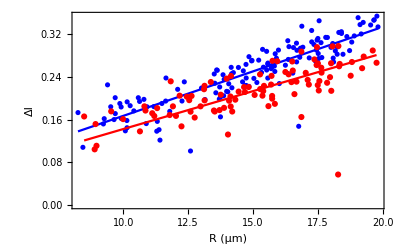

```mathematica
showScatterPlot[]
```

```mathematica
(*estimate derivateive vaues*)
dSlopes = slope1 - slope0;
errdSlopes = Abs[dSlopes] √((errSlope0/slope0)^2+(errSlope1/slope1)^2);
```

```mathematica
Grid[{
{"Name", "Value", "Error", "STD"},
{"Velocity", Mean[v], StandardError[v], StandardDeviation[v]},
{"Slope t=0", slope0 , errSlope0, σ0},
{"Slope t=1", slope1 , errSlope1, σ1},
{"Δc/c_0", -dSlopes*h/2 , errdSlopes*h/2, ""}
}, Frame->All,Alignment->"."]
```

Name | Value | Error | STD
Velocity | 0.768378 | 0.00997498 | 0.153886
Slope t=0 | 0.0166884 | 0.000838571 | 0.0269776
Slope t=1 | 0.0142193 | 0.00130507 | 0.0331928
Δc/c_0 | 0.049383 | 0.00516726 |

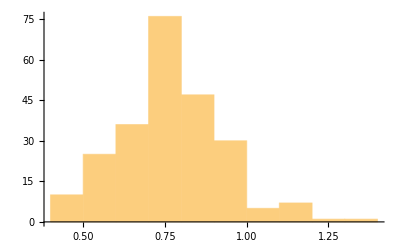

```mathematica
v//Histogram
```

```mathematica
aprxError = σ0/(√Length[r0])/ Mean[r0]
```

## User Friendly interface

Remember to format data into single CSV file with two sets following each other. An Example:
Radius,AvgDF,Velocity,Radius,AvgDF,Velocity
19.16671875,0.3205,0.769,16.5965625,0.2077,0.748
19.66734375,0.3469,0.839,16.86421875,0.1648,0.523
...

```mathematica
userFriendlyInterface[] (*run by clicking Shift-Enter*)
```

Channel Height (μm) | 
Distance (μm) | 
Input File | 
 | Do the Magic!

loaded file: data/formated_data.csv

-Graphics-

Name | Value | Error | STD
Velocity | 0.768378 | 0.00997498 | 0.153886
Slope t=0 | 0.0166884 | 0.000838571 | 0.0269776
Slope t=1 | 0.0142193 | 0.00130507 | 0.0331928
Δc/c_0 | 0.049383 | -0.00516726 |